## Runge - Kutta

```mathematica
(*Ecuación Diferencial:*)
Eq=y'[t]==y[t]Sin[t];
(*Condición *)
Ci=y[0]==-1;
```

```mathematica
sol=NDSolve[Join[{Eq,Ci}],y,{t,0,1000},StepMonitor:>Sow[x],Method-> {"ExplicitRungeKutta","DifferenceOrder"-> 4},MaxSteps-> 10^8,AccuracyGoal-> 15];
```

```mathematica
(*solución para el tiempo 40*)
y[t]/.sol/.t-> 40
```

{-5.29593}

### Tabulación de soluciones

```mathematica
np=10^1;τ=100*np;(*τ=tiempo a evaluar*)
Monitor[soluciones=Table[Flatten[{N[t],y[t]}/.sol/.t-> k/np],{k,0,τ}],ProgressIndicator[N[k/τ]]];
Export["RK4-Mathem.txt",soluciones];
```

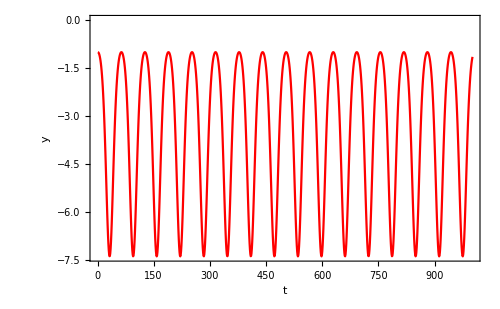

```mathematica
ListPlot[soluciones[[1;;-1,2]],Joined-> True,PlotStyle-> Red ,ImageSize->500,Axes->False,Frame->True,FrameLabel->{Style["t",20],Style["y",20]},LabelStyle->Directive[16]]
```

```mathematica
soluciones[[601,2]]
solpy[[1600]]
```

-7.04567

{-7.12670966350481727}

```mathematica
solpy=Import["RK4_python.txt","Table"];
```

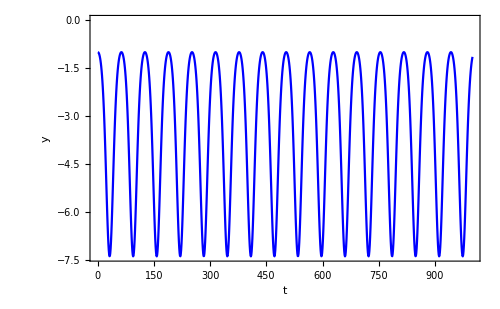

```mathematica
ListPlot[Flatten[solpy[[1001;;2000]]],Joined-> True,PlotStyle-> Blue ,ImageSize->500,Axes->False,Frame->True,FrameLabel->{Style["t",20],Style["y",20]},LabelStyle->Directive[16]]
```

```mathematica
Dimensions[soluciones]
```

{1001,1,2}

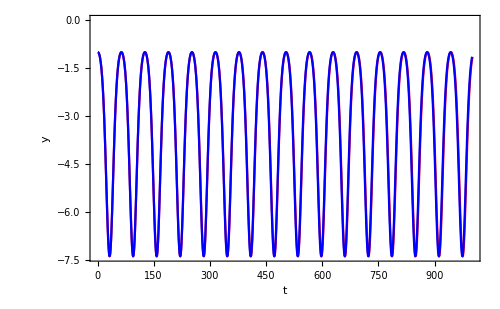

```mathematica
Show[%98,%72]
```